# octet.experiment.rencon1.figure.lambda-merge.style-5.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.paper.chpt.ed12\octet.experiment.rencon1.figure.lambda-merge.style-5.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

gegm`normal`lightsea |  blue | solid
gegm`normal`strange | red | solid
gegm`degeneracy`lightsea | Black | dotted
gegm`masslimit`lightsea | Orange | dashed
gegm`degeneracy`strange | Red | dotted
gegm`masslimit`lightsea | Red | dashed

normal

```mathematica
fig`calc`nucleon`normal`ge`u = {0, 0, 0};
fig`calc`nucleon`normal`ge`d = {0, 0, 0};
fig`calc`nucleon`normal`ge`s = {0, 0, 0};
```

```mathematica
fig`calc`nucleon`normal`gm`u = {0, 0, 0};
fig`calc`nucleon`normal`gm`d = {0, 0, 0};
fig`calc`nucleon`normal`gm`s = {0, 0, 0};
```

degeneracy

```mathematica
fig`calc`nucleon`degeneracy`ge`u = {0, 0, 0};
fig`calc`nucleon`degeneracy`ge`d = {0, 0, 0};
fig`calc`nucleon`degeneracy`ge`s = {0, 0, 0};
```

```mathematica
fig`calc`nucleon`degeneracy`gm`u = {0, 0, 0};
fig`calc`nucleon`degeneracy`gm`d = {0, 0, 0};
fig`calc`nucleon`degeneracy`gm`s = {0, 0, 0};
```

degeneracy

```mathematica
fig`calc`nucleon`masslimit`ge`u = {0, 0, 0};
fig`calc`nucleon`masslimit`ge`d = {0, 0, 0};
fig`calc`nucleon`masslimit`ge`s = {0, 0, 0};
```

```mathematica
fig`calc`nucleon`masslimit`gm`u = {0, 0, 0};
fig`calc`nucleon`masslimit`gm`d = {0, 0, 0};
fig`calc`nucleon`masslimit`gm`s = {0, 0, 0};
```

style

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[1],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
style`calc={
AbsoluteThickness[_]-> AbsoluteThickness[1]
};
```

```mathematica
directory`fig="C:\\Users\\Tom\\Desktop\\octet.fig";
```

## nucleon`ge`light-sea

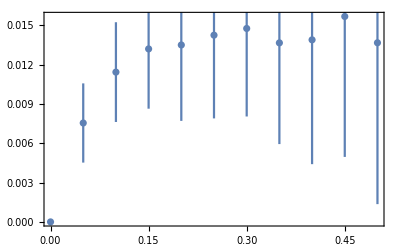
```mathematica
fig`exp`nucleon`ge`lightsea=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

fig`calc`nucleon`normal`ge

## fig`calc`nucleon`ge`u

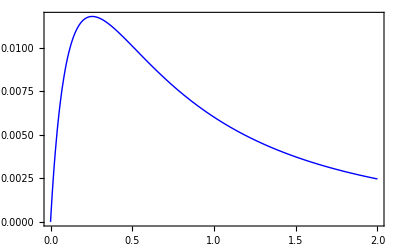

```mathematica
fig`calc`nucleon`normal`ge`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

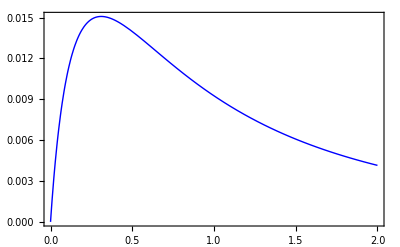

```mathematica
fig`calc`nucleon`normal`ge`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

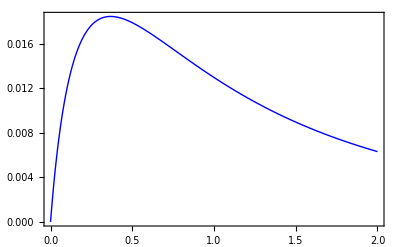

```mathematica
fig`calc`nucleon`normal`ge`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

## fig`calc`nucleon`ge`d

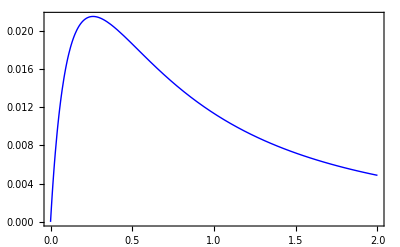

```mathematica
fig`calc`nucleon`normal`ge`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

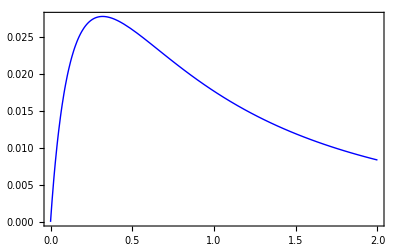

```mathematica
fig`calc`nucleon`normal`ge`d⟦2⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue)
```

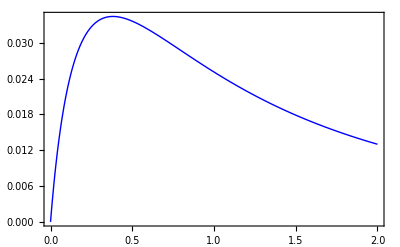

```mathematica
fig`calc`nucleon`normal`ge`d⟦3⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue)
```

fig`calc`nucleon`degeneracy`ge

## fig`calc`nucleon`degeneracy`ge`u

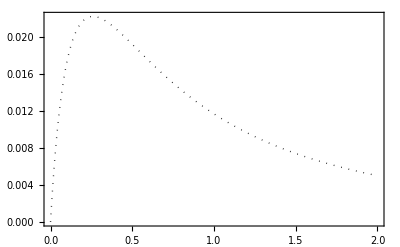

```mathematica
fig`calc`nucleon`degeneracy`ge`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

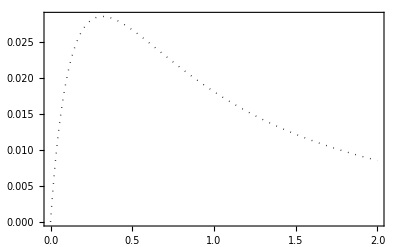

```mathematica
fig`calc`nucleon`degeneracy`ge`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

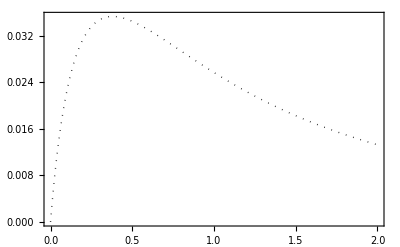

```mathematica
fig`calc`nucleon`degeneracy`ge`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

## fig`calc`nucleon`degeneracy`ge`d

```mathematica
fig`calc`nucleon`degeneracy`ge`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

-Graphics-

```mathematica
fig`calc`nucleon`degeneracy`ge`d⟦2⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black)
```

-Graphics-

```mathematica
fig`calc`nucleon`degeneracy`ge`d⟦3⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black)
```

-Graphics-

fig`calc`nucleon`masslimit`ge

## fig`calc`nucleon`masslimit`ge`u

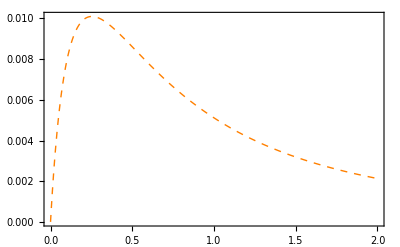

```mathematica
fig`calc`nucleon`masslimit`ge`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

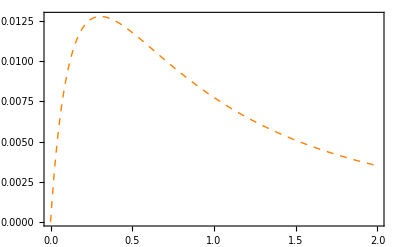

```mathematica
fig`calc`nucleon`masslimit`ge`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

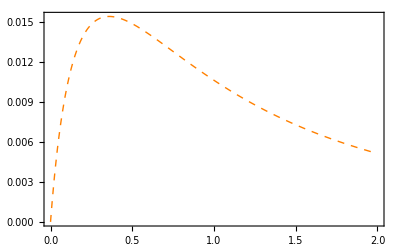

```mathematica
fig`calc`nucleon`masslimit`ge`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

## fig`calc`nucleon`masslimit`ge`d

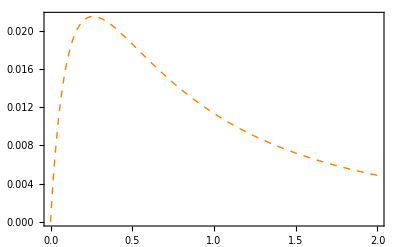

```mathematica
fig`calc`nucleon`masslimit`ge`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

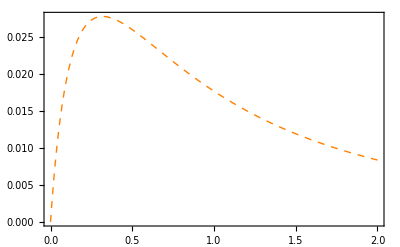

```mathematica
fig`calc`nucleon`masslimit`ge`d⟦2⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange)
```

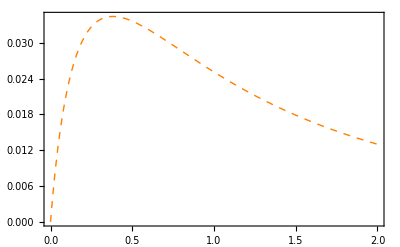

```mathematica
fig`calc`nucleon`masslimit`ge`d⟦3⟧=(Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange)
```

fig`comparison`normal`ge

## fig`comparison`ge`u

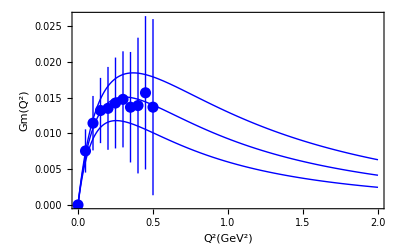

```mathematica
fig`comparison`normal`ge`u=Show[
{
fig`exp`nucleon`ge`lightsea,

fig`calc`nucleon`normal`ge`u⟦1⟧,fig`calc`nucleon`normal`ge`u⟦2⟧,fig`calc`nucleon`normal`ge`u⟦3⟧

},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`normal`ge`d

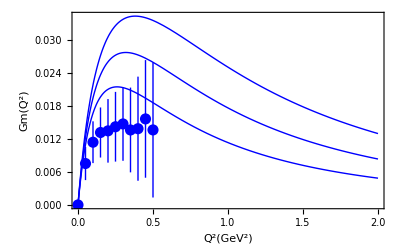

```mathematica
fig`comparison`normal`ge`d=Show[
{
fig`exp`nucleon`ge`lightsea,

fig`calc`nucleon`normal`ge`d⟦1⟧,fig`calc`nucleon`normal`ge`d⟦2⟧,fig`calc`nucleon`normal`ge`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`degeneracy`ge

## fig`comparison`degeneracy`ge`u

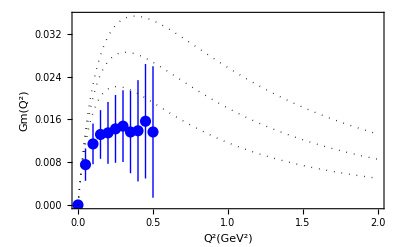

```mathematica
fig`comparison`degeneracy`ge`u=Show[
{
fig`exp`nucleon`ge`lightsea,
fig`calc`nucleon`degeneracy`ge`u⟦1⟧,
fig`calc`nucleon`degeneracy`ge`u⟦2⟧,
fig`calc`nucleon`degeneracy`ge`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`degeneracy`ge`d

```mathematica
fig`comparison`ge`d=Show[
{fig`exp`nucleon`ge`lightsea,
fig`calc`nucleon`degeneracy`ge`d⟦1⟧,
fig`calc`nucleon`degeneracy`ge`d⟦2⟧,fig`calc`nucleon`degeneracy`ge`d⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

fig`comparison`masslimit`ge

## fig`comparison`masslimit`ge`u

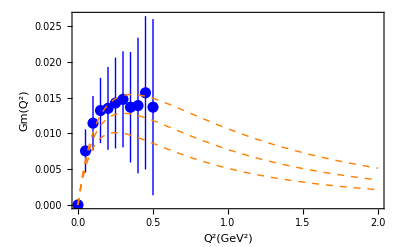

```mathematica
fig`comparison`masslimit`ge`u=Show[
{fig`exp`nucleon`ge`lightsea,
fig`calc`nucleon`masslimit`ge`u⟦1⟧,
fig`calc`nucleon`masslimit`ge`u⟦2⟧,
fig`calc`nucleon`masslimit`ge`u⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`masslimit`ge`d

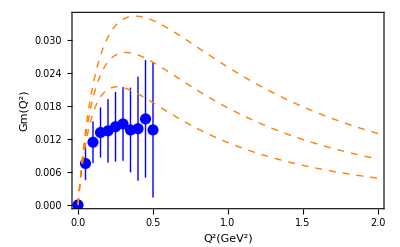

```mathematica
fig`comparison`ge`d=Show[
{fig`exp`nucleon`ge`lightsea,
fig`calc`nucleon`masslimit`ge`d⟦1⟧,
fig`calc`nucleon`masslimit`ge`d⟦2⟧,fig`calc`nucleon`masslimit`ge`d⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`ge`strange

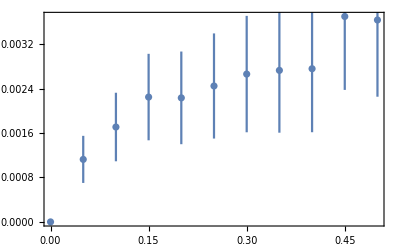
```mathematica
fig`exp`nucleon`ge`s=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Red;
```

fig`calc`nucleon`normal`ge

## fig`calc`nucleon`normal`ge`s

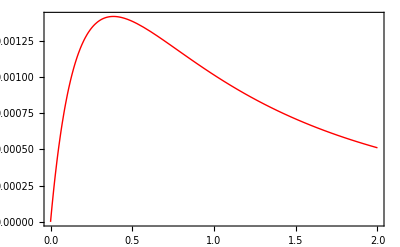

```mathematica
fig`calc`nucleon`normal`ge`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

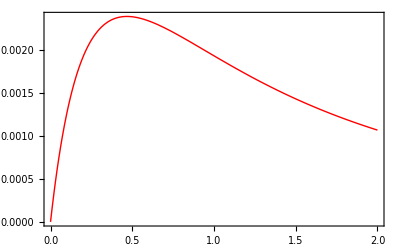

```mathematica
fig`calc`nucleon`normal`ge`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

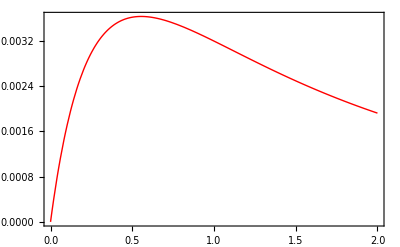

```mathematica
fig`calc`nucleon`normal`ge`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.ge.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`calc`nucleon`degeneracy`ge`s

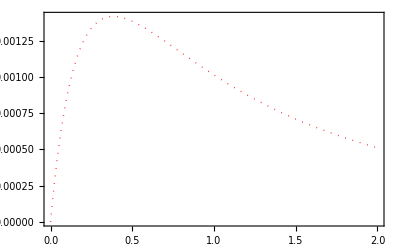

```mathematica
fig`calc`nucleon`degeneracy`ge`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

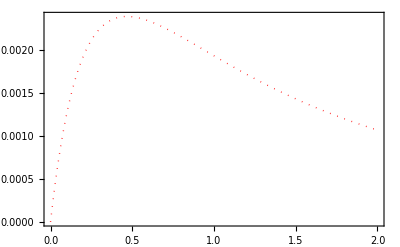

```mathematica
fig`calc`nucleon`degeneracy`ge`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

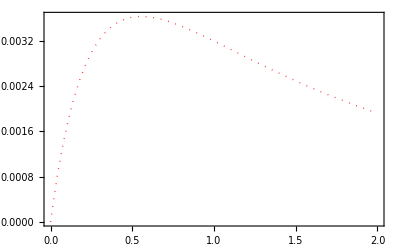

```mathematica
fig`calc`nucleon`degeneracy`ge`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.ge.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`calc`nucleon`masslimit`ge`s

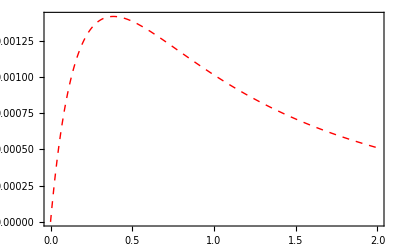

```mathematica
fig`calc`nucleon`masslimit`ge`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

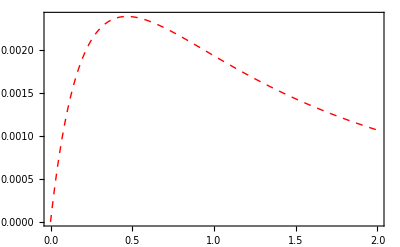

```mathematica
fig`calc`nucleon`masslimit`ge`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

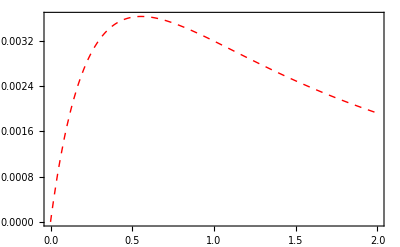

```mathematica
fig`calc`nucleon`masslimit`ge`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.ge.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`comparison`ge`s

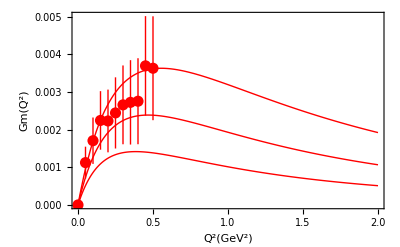

```mathematica
fig`comparison`normal`ge`s=Show[
{
fig`exp`nucleon`ge`s,
fig`calc`nucleon`normal`ge`s⟦1⟧,fig`calc`nucleon`normal`ge`s⟦2⟧,fig`calc`nucleon`normal`ge`s⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`degeneracy`ge`s

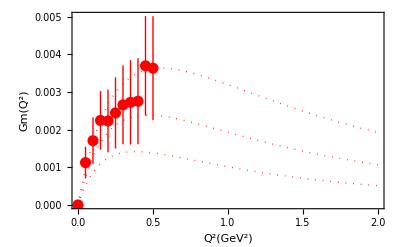

```mathematica
fig`comparison`degeneracy`ge`s=Show[
{fig`exp`nucleon`ge`s,
fig`calc`nucleon`degeneracy`ge`s⟦1⟧,
fig`calc`nucleon`degeneracy`ge`s⟦2⟧,fig`calc`nucleon`degeneracy`ge`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`masslimit`ge`s

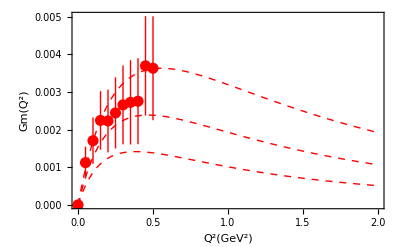

```mathematica
fig`comparison`masslimit`ge`s=Show[
{fig`exp`nucleon`ge`s,
fig`calc`nucleon`masslimit`ge`s⟦1⟧,
fig`calc`nucleon`masslimit`ge`s⟦2⟧,fig`calc`nucleon`masslimit`ge`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`gm`lightsea

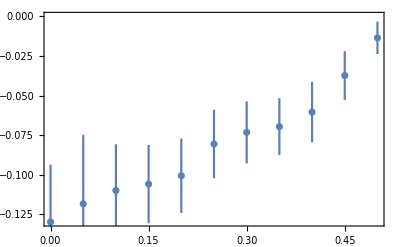
```mathematica
fig`exp`nucleon`gm`lightsea=
-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Blue;
```

fig`calc`nucleon`normal`gm`normal

## fig`calc`nucleon`gm`u

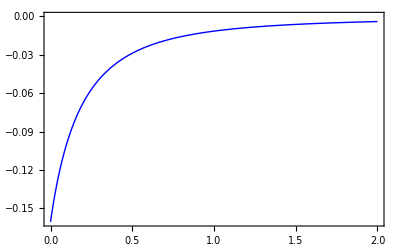

```mathematica
fig`calc`nucleon`normal`gm`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

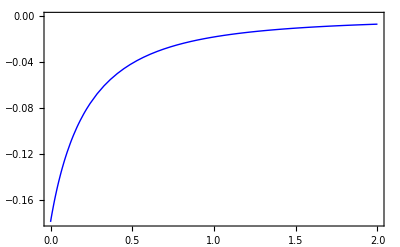

```mathematica
fig`calc`nucleon`normal`gm`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

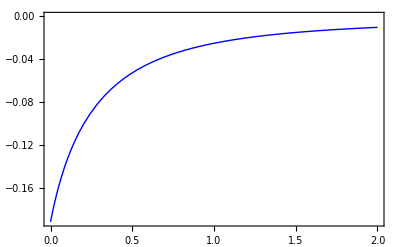

```mathematica
fig`calc`nucleon`normal`gm`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

## fig`calc`nucleon`gm`d

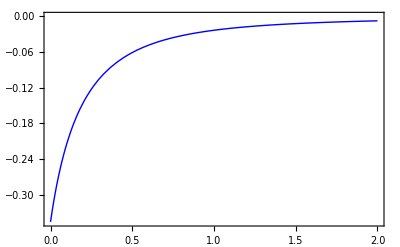

```mathematica
fig`calc`nucleon`normal`gm`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

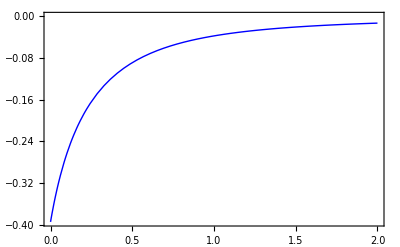

```mathematica
fig`calc`nucleon`normal`gm`d⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

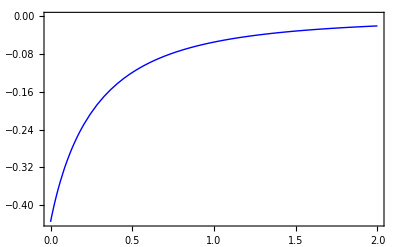

```mathematica
fig`calc`nucleon`normal`gm`d⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Blue
```

fig`calc`nucleon`degeneracy`gm

## fig`calc`nucleon`degeneracy`gm`u

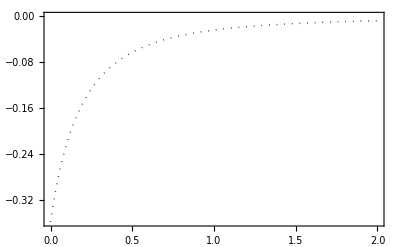

```mathematica
fig`calc`nucleon`degeneracy`gm`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

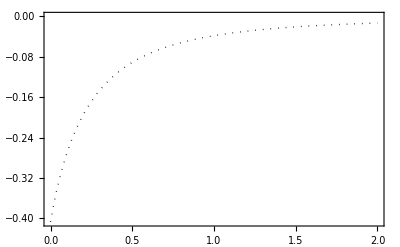

```mathematica
fig`calc`nucleon`degeneracy`gm`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

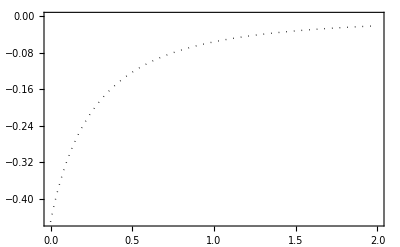

```mathematica
fig`calc`nucleon`degeneracy`gm`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

## fig`calc`nucleon`degeneracy`gm`d

```mathematica
fig`calc`nucleon`degeneracy`gm`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

-Graphics-

```mathematica
fig`calc`nucleon`degeneracy`gm`d⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

-Graphics-

```mathematica
fig`calc`nucleon`degeneracy`gm`d⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Black
```

-Graphics-

fig`calc`nucleon`masslimit`gm

## fig`calc`nucleon`masslimit`gm`u

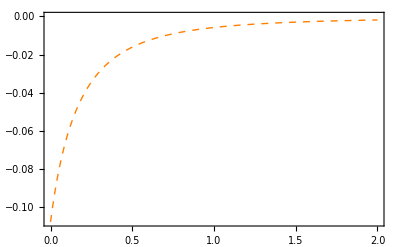

```mathematica
fig`calc`nucleon`masslimit`gm`u⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.u.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

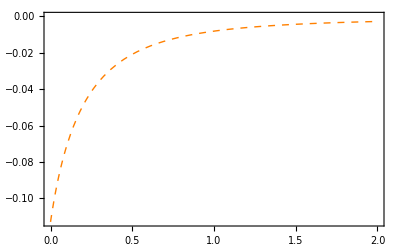

```mathematica
fig`calc`nucleon`masslimit`gm`u⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.u.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

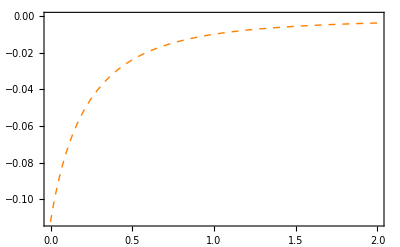

```mathematica
fig`calc`nucleon`masslimit`gm`u⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.u.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

## fig`calc`nucleon`masslimit`gm`d

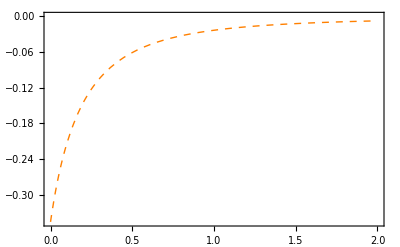

```mathematica
fig`calc`nucleon`masslimit`gm`d⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.d.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

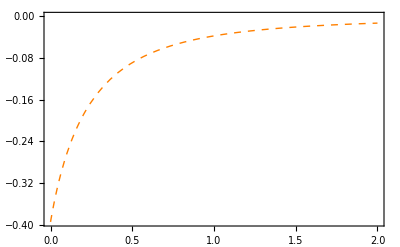

```mathematica
fig`calc`nucleon`masslimit`gm`d⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.d.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

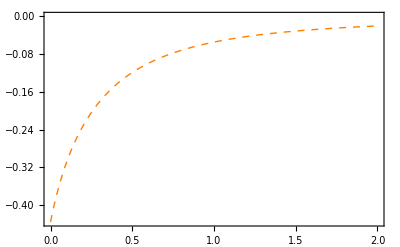

```mathematica
fig`calc`nucleon`masslimit`gm`d⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.d.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Orange
```

fig`comparison`noraml`gm`u

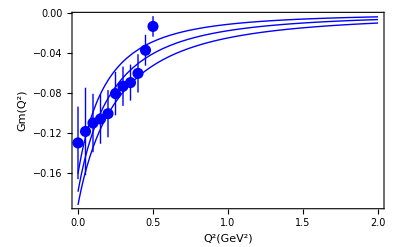

```mathematica
fig`comparison`normal`gm`u=Show[
{
fig`exp`nucleon`gm`lightsea,

fig`calc`nucleon`normal`gm`u⟦1⟧,fig`calc`nucleon`normal`gm`u⟦2⟧,fig`calc`nucleon`normal`gm`u⟦3⟧

},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`normal`gm`d

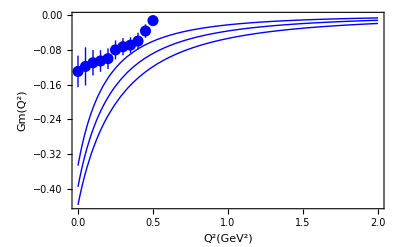

```mathematica
fig`comparison`normal`gm`d=Show[
{
fig`exp`nucleon`gm`lightsea,

fig`calc`nucleon`normal`gm`d⟦1⟧,fig`calc`nucleon`normal`gm`d⟦2⟧,fig`calc`nucleon`normal`gm`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`degeneracy`gm

## fig`comparison`degeneracy`gm`u

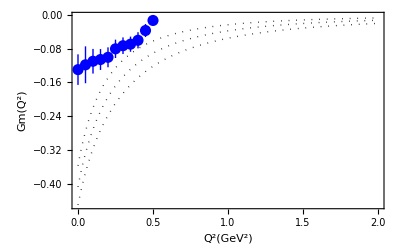

```mathematica
fig`comparison`degeneracy`gm`u=Show[
{
fig`exp`nucleon`gm`lightsea,
fig`calc`nucleon`degeneracy`gm`u⟦1⟧,
fig`calc`nucleon`degeneracy`gm`u⟦2⟧,fig`calc`nucleon`degeneracy`gm`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`degeneracy`gm`d

```mathematica
fig`comparison`degeneracy`gm`d=Show[
{
fig`exp`nucleon`gm`lightsea,
fig`calc`nucleon`degeneracy`gm`d⟦1⟧,
fig`calc`nucleon`degeneracy`gm`d⟦2⟧,fig`calc`nucleon`degeneracy`gm`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

-Graphics-

fig`comparison`masslimit`gm

## fig`comparison`masslimit`gm`u

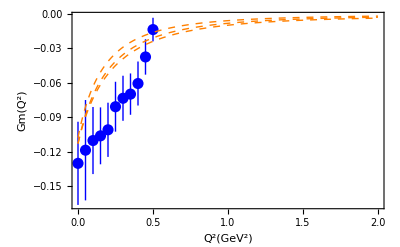

```mathematica
fig`comparison`masslimit`gm`u=Show[
{
fig`exp`nucleon`gm`lightsea,

fig`calc`nucleon`masslimit`gm`u⟦1⟧,
fig`calc`nucleon`masslimit`gm`u⟦2⟧,fig`calc`nucleon`masslimit`gm`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## fig`comparison`masslimit`gm`d

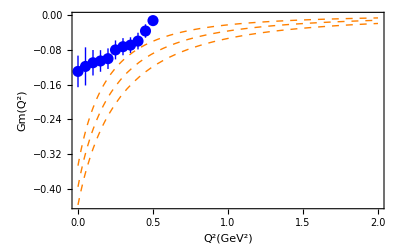

```mathematica
fig`comparison`masslimit`gm`d=Show[
{
fig`exp`nucleon`gm`lightsea,
fig`calc`nucleon`masslimit`gm`d⟦1⟧,
fig`calc`nucleon`masslimit`gm`d⟦2⟧,fig`calc`nucleon`masslimit`gm`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## nucleon`gm`strange

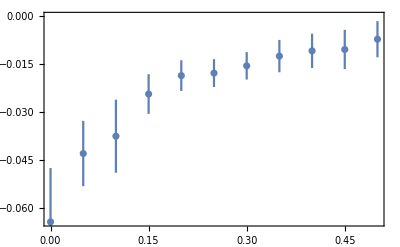
```mathematica
fig`exp`nucleon`gm`s=-Graphics-/.style`exp/.RGBColor[0.368417,0.506779,0.709798]->Red;
```

fig`calc`nucleon`normal`gm`s

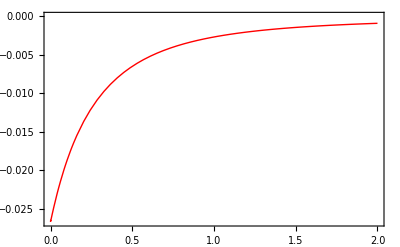

```mathematica
fig`calc`nucleon`normal`gm`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

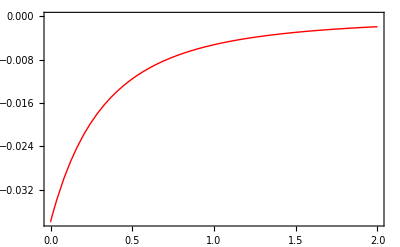

```mathematica
fig`calc`nucleon`normal`gm`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

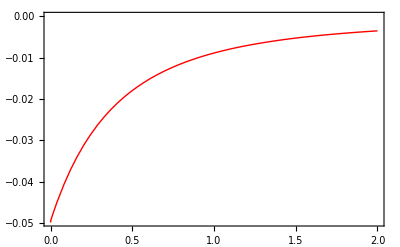

```mathematica
fig`calc`nucleon`normal`gm`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.gm.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`calc`nucleon`degeneracy`gm`s

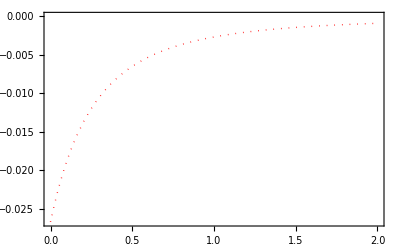

```mathematica
fig`calc`nucleon`degeneracy`gm`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

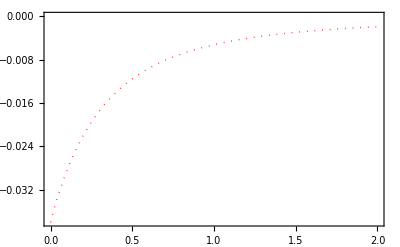

```mathematica
fig`calc`nucleon`degeneracy`gm`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

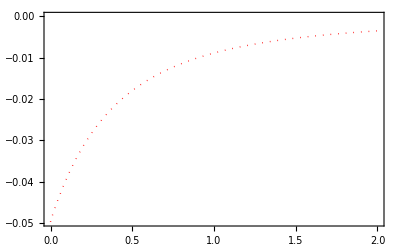

```mathematica
fig`calc`nucleon`degeneracy`gm`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.degeneracy.gm.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`calc`nucleon`masslimit`gm`s

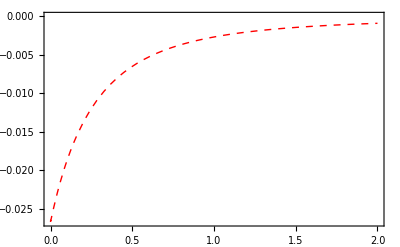

```mathematica
fig`calc`nucleon`masslimit`gm`s⟦1⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.s.L-0.80.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

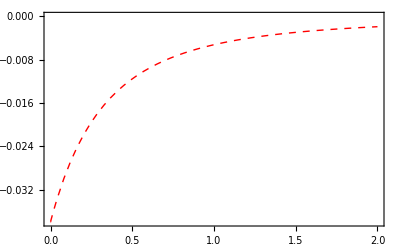

```mathematica
fig`calc`nucleon`masslimit`gm`s⟦2⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.s.L-0.90.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

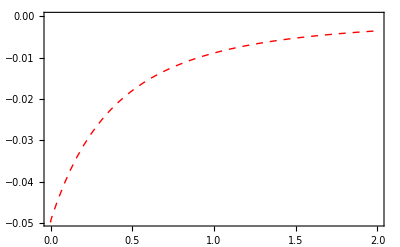

```mathematica
fig`calc`nucleon`masslimit`gm`s⟦3⟧=Get[
FileNameJoin[{directory`fig,
"fig.calc.nucleon.masslimit.gm.s.L-1.00.m"}]
]/.style`calc/."Loop"->""/.RGBColor[0.368417,0.506779,0.709798]->Red
```

fig`comparison`normal`gm`s

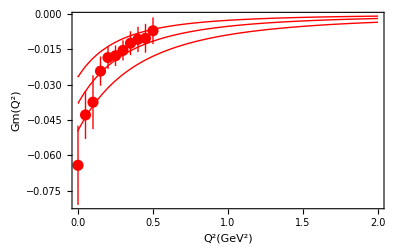

```mathematica
fig`comparison`normal`gm`s=Show[
{

fig`exp`nucleon`gm`s,

fig`calc`nucleon`normal`gm`s⟦1⟧,
fig`calc`nucleon`normal`gm`s⟦2⟧,fig`calc`nucleon`normal`gm`s⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`degeneracy`gm`s

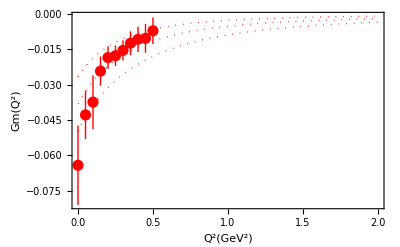

```mathematica
fig`comparison`degeneracy`gm`s=Show[
{
fig`exp`nucleon`gm`s,

fig`calc`nucleon`degeneracy`gm`s⟦1⟧,
fig`calc`nucleon`degeneracy`gm`s⟦2⟧,fig`calc`nucleon`degeneracy`gm`s⟦3⟧},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

fig`comparison`masslimit`gm`s

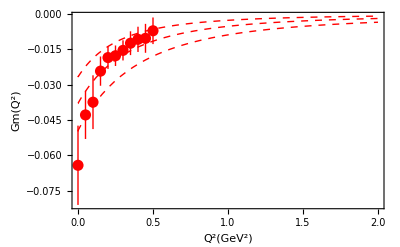

```mathematica
fig`comparison`masslimit`gm`s=Show[
{
fig`exp`nucleon`gm`s,

fig`calc`nucleon`masslimit`gm`s⟦1⟧,
fig`calc`nucleon`masslimit`gm`s⟦2⟧,fig`calc`nucleon`masslimit`gm`s⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

## gegm sea u, d, s

ge u and s

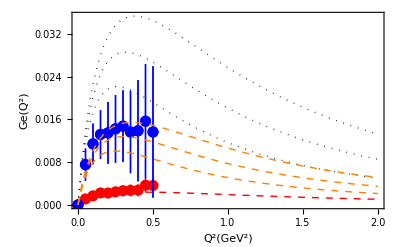
-Graphics-Ge of u and strange

```mathematica
fig`labled`comparison`paper`ge`us=Labeled[
fig`comparison`paper`ge`us=Show[
{
fig`exp`nucleon`ge`s,(*experimental strange*)
fig`calc`nucleon`masslimit`ge`s⟦2⟧,

fig`exp`nucleon`ge`lightsea,(*experimental lightsea*)

fig`calc`nucleon`degeneracy`ge`u⟦1⟧,
fig`calc`nucleon`degeneracy`ge`u⟦2⟧,fig`calc`nucleon`degeneracy`ge`u⟦3⟧,

fig`exp`nucleon`ge`lightsea,fig`calc`nucleon`masslimit`ge`u⟦1⟧,
fig`calc`nucleon`masslimit`ge`u⟦2⟧,fig`calc`nucleon`masslimit`ge`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->{
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
},
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
}
},
FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Ge of u and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

ge d and s

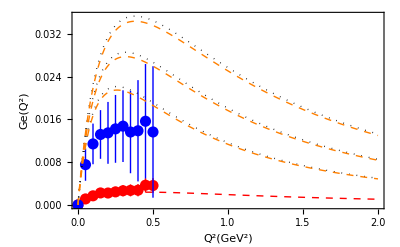
-Graphics-Ge of d and strange

```mathematica
fig`labled`comparison`paper`ge`ds=Labeled[
fig`comparison`paper`ge`ds=Show[
{
fig`exp`nucleon`ge`s,(*experimental strange*)
fig`calc`nucleon`masslimit`ge`s⟦2⟧,

fig`exp`nucleon`ge`lightsea,(*experimental lightsea*)

fig`calc`nucleon`degeneracy`ge`d⟦1⟧,fig`calc`nucleon`degeneracy`ge`d⟦2⟧,
fig`calc`nucleon`degeneracy`ge`d⟦3⟧,

fig`calc`nucleon`masslimit`ge`d⟦1⟧,fig`calc`nucleon`masslimit`ge`d⟦2⟧,
fig`calc`nucleon`masslimit`ge`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->{
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
},
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
}
},
FrameLabel->{
{Style["Ge(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Ge of d and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm u and s

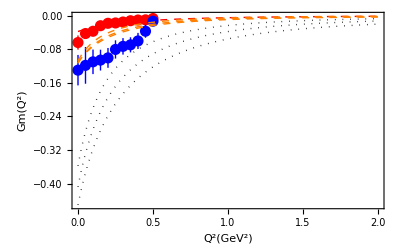
-Graphics-Gm of u and strange

```mathematica
fig`labled`comparison`paper`gm`us=Labeled[
fig`comparison`paper`gm`us=Show[
{
fig`exp`nucleon`gm`s,(*experimental strange*)
fig`calc`nucleon`masslimit`gm`s⟦2⟧,

fig`exp`nucleon`gm`lightsea,(*experimental lightsea*)

fig`calc`nucleon`degeneracy`gm`u⟦1⟧,
fig`calc`nucleon`degeneracy`gm`u⟦2⟧,fig`calc`nucleon`degeneracy`gm`u⟦3⟧,

fig`calc`nucleon`masslimit`gm`u⟦1⟧,
fig`calc`nucleon`masslimit`gm`u⟦2⟧,fig`calc`nucleon`masslimit`gm`u⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->{
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
},
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
}
},
FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Gm of u and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm d and s

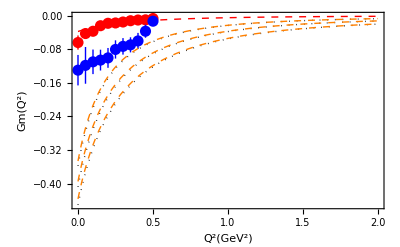
-Graphics-Gm of d and strange

```mathematica
fig`labled`comparison`paper`gm`ds=Labeled[
fig`comparison`paper`gm`ds=Show[
{
fig`exp`nucleon`gm`s,(*experimental strange*)
fig`calc`nucleon`masslimit`gm`s⟦2⟧,

fig`exp`nucleon`gm`lightsea,(*experimental lightsea*)

fig`calc`nucleon`degeneracy`gm`d⟦1⟧,
fig`calc`nucleon`degeneracy`gm`d⟦2⟧,fig`calc`nucleon`degeneracy`gm`d⟦3⟧,

fig`calc`nucleon`masslimit`gm`d⟦1⟧,
fig`calc`nucleon`masslimit`gm`d⟦2⟧,fig`calc`nucleon`masslimit`gm`d⟦3⟧
},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True,
FrameStyle->{
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
},
{
Directive[AbsoluteThickness[1.5],Black],
Directive[AbsoluteThickness[1.5],Black]
}
},
FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
,"Gm of d and strange"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

fig`sea`us`gegm

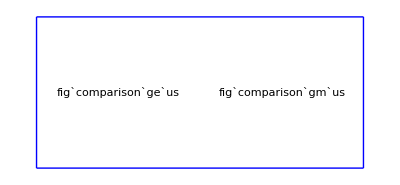
-Graphics-Ge (left side) and Gm (right side)

```mathematica
fig`sea`us`gegm=Labeled[
GraphicsGrid[
{{fig`comparison`ge`us,fig`comparison`gm`us}},
Spacings->{Scaled[.2],Scaled[.1]},
ImageSize->Scaled[.75],
AspectRatio->Automatic,
ItemAspectRatio->Automatic,
Frame->True,
FrameStyle->Directive[Blue,FontSize->10]
,Alignment->{Center,Center}
]
,"Ge (left side) and Gm (right side)"
,{{Bottom,Center}}
,LabelStyle->{"Section",FontSize-> 14}
]
```

gm`normal u & d

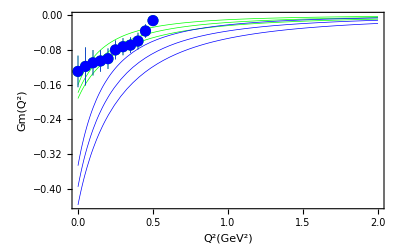

```mathematica
Show[
{fig`comparison`gm`u/.Blue->Black,fig`comparison`gm`d},
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Automatic}},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
,FrameLabel->{
{Style["Gm(Q^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None},
{Style["Q^2(GeV^2)",FontFamily->"Microsoft YaHei UI",FontSize->9],None}
}
]
```

export

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-results/"}]]
```

```mathematica
Export["fig3.eps",fig`labled`comparison`paper`ge`us];
Export["fig4.eps",fig`labled`comparison`paper`gm`us];
```

```mathematica
Export["fig5.eps",fig`labled`comparison`paper`ge`ds];
Export["fig6.eps",fig`labled`comparison`paper`gm`ds];
```